## Basic math facts

```mathematica
Integrate[Log[1+Exp[-x]],x]
```

PolyLog[2,-ⅇ^-x]

```mathematica
PolyLog[2,0]
```

0

```mathematica
PolyLog[2,-Infinity]
```

-∞

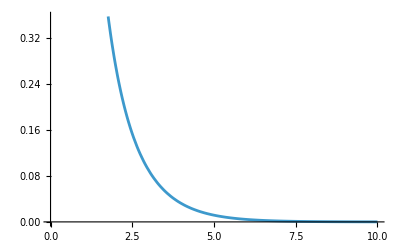

```mathematica
ΔPL=PolyLog[2,Exp[-b*(x-u)]]-PolyLog[2,Exp[-b*x]];
Plot[ΔPL/.{b->1,u->1},{x,0,10}]
```

## Grand potential

```mathematica
Gsys=LS*Integrate[Log[1+Exp[-β*(x-μ)]],{x,-Λ,Infinity},Assumptions->{Λ>0,μ∈Reals,β>0}]
Gsys0=LS*Integrate[Log[1+Exp[-β*x]],{x,-Λ,Infinity},Assumptions->{Λ>0,β>0}](*So we see that the μ=0 case is actually also included in Gsys*)
```

ConditionalExpression[-(LS PolyLog[2,-ⅇ^(β (Λ+μ))])/β, μ≠0]

-(LS PolyLog[2,-ⅇ^(β Λ)])/β

```mathematica
GsysAll=Simplify[Gsys,Assumptions->μ≠0];
ΔGsys=GsysAll-Gsys0;
Grsv=LR*Log[1+Exp[β*μ]];
Gjalim=ΔGsys+Grsv
```

LR Log[1+ⅇ^(β μ)]+(LS PolyLog[2,-ⅇ^(β Λ)])/β-(LS PolyLog[2,-ⅇ^(β (Λ+μ))])/β

Getting stuck here.

```mathematica
Gj=Limit[Gjalim/.aList,Λ->Infinity,Assumptions->{μ∈Reals,β>0,LS>0,LR>0}]
```

μ ∞

```mathematica
JparamsList={LS->1,LR->1(*,β->1*)};
Gjp=Gj/.JparamsList/.aList
```

Log[1+ⅇ^(β μ)]

Invert β to S.

(ⅇ^(β μ) β^2 μ)/(1+ⅇ^(β μ))

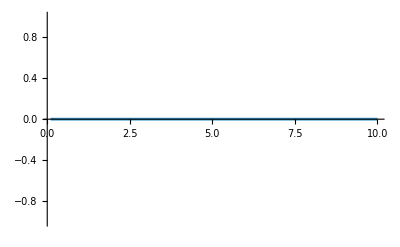

```mathematica
sFromGjp=β^2*D[Gjp,β]
Plot[sFromGjp/.μ->0,{β,0.1,10}]
```

-0.5 β+(ⅇ^(β μ) β)/(1+ⅇ^(β μ))

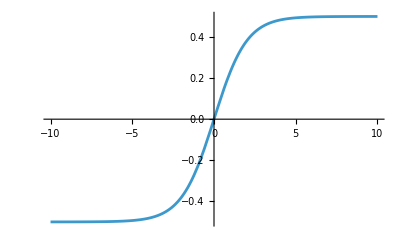

```mathematica
βRule=β->1;
navg=D[Gjp,μ]-0.5*β
navgβ=navg/.βRule;
Plot[navgβ,{μ,-10,10}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Log[(-1.-2. n)/(-1.+2. n)]

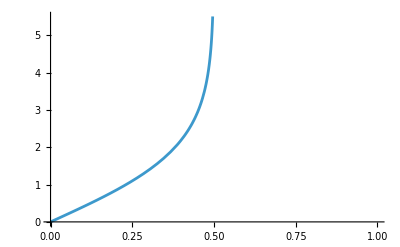

```mathematica
μFromnavgβ=μ/.Solve[navgβ==n,μ][[1]]
Plot[μFromnavgβ,{n,0,1}]
```

Log[-1./(-0.5+1. n)]

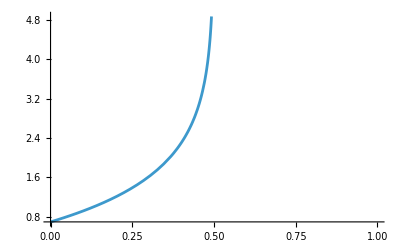

```mathematica
GjpOfn=Simplify[Gjp/.μ->μFromnavgβ/.βRule]
Plot[GjpOfn,{n,0,1}]
```